```mathematica
Clear[t]
```

```mathematica
getPath[x_,imp_,f_,βp_]:=
Module[{tsnond,nondeqnsb,nondbcsb,nondeqnsc,nondbcsc,solc,dom,maxh,solb,bpath,tc,cpath},

tsnond := N[imp/f];

(*Solve boost phase*)
nondeqnsb={h'[t] == v[t],
 v'[t] == (f-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == -f};

nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};

solb=Evaluate[NDSolve[({nondeqnsb, nondbcsb})//Flatten,{h[t],v[t],m[t]},{t, 0.0, tsnond}]];
bpath = Table[{t,(h[t]/.solb[[1]])},{t,0,tsnond,tsnond/100}];

(*Solve coast phase*)
nondeqnsc={h'[t] == v[t],
 v'[t] == (-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == 0};

nondbcsc = {h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond],
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond],
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]};

solc=Evaluate[Quiet[NDSolve[{nondeqnsc, nondbcsc}//Flatten,{h[t],v[t],m[t]},{t,  tsnond, 20*tsnond}]]];



tc = FindArgMax[h[t]/.solc[[1]],{t,tsnond}][[1]];
cpath = Table[{t,(h[t]/.solc[[1]])},{t,tsnond,tc, (tc-tsnond)/100}];



path = Join[bpath,cpath]]

(*
(*Find apogee*)
dom=solc[[1]][[1]][[2]][[0]]["Domain"][[1]];
maxh=FindMaxValue[{solc[[1]][[1]][[2]],dom[[1]]<t<dom[[2]]},t]]*)
```

```mathematica
getH[x_,imp_,f_,βp_]:=
Module[{h,v,m,t,tsnond,nondeqnsb,nondbcsb,nondeqnsc,nondbcsc,solc,dom,maxh,solb,tc,h},

tsnond := N[imp/f];

(*Solve boost phase*)
nondeqnsb={h'[t] == v[t],
 v'[t] == (f-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == -f};

nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};

solb=Evaluate[NDSolve[({nondeqnsb, nondbcsb})//Flatten,{h[t],v[t],m[t]},{t, 0.0, tsnond}]];

(*Solve coast phase*)
nondeqnsc={h'[t] == v[t],
 v'[t] == (-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == 0};

nondbcsc = {h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond],
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond],
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]};

solc=Evaluate[Quiet[NDSolve[{nondeqnsc, nondbcsc}//Flatten,{h[t],v[t],m[t]},{t,  tsnond, 20*tsnond}]]];



tc = FindArgMax[h[t]/.solc[[1]],{t,tsnond}][[1]];
h = ((h[t]/.solc[[1]])/.t-> tc)]
```

```mathematica
h = getH[70,0.15,2,50]
```

0.00537997

```mathematica
getH[70,0.15,6,50]
```

0.00703009

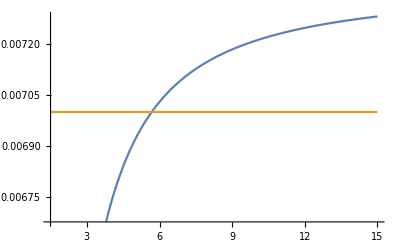

```mathematica
Plot[{getH[70,0.15,f,50],0.007},{f,1.5,15}]
```

```mathematica
NSolve[Abs[getH[70,imp,6,50]-0.007],{imp,0.15}]
```

NSolve[Abs[-0.007+Module[{h$,v$,m$,t$,tsnond$,nondeqnsb$,nondbcsb$,nondeqnsc$,nondbcsc$,solc$,dom$,maxh$,solb$,tc$,h$},tsnond$:=N[imp/6];nondeqnsb$={h$'[t$]==v$[t$],v$'[t$]==(6-70 Exp[-50 h$[t$]] v$[t$]^2)/m$[t$]-1,m$'[t$]==-6};nondbcsb$={h$[0]==0,v$[0]==0,m$[0]==1};solb$=Evaluate[NDSolve[Flatten[{nondeqnsb$,nondbcsb$}],{h$[t$],v$[t$],m$[t$]},{t$,0.,tsnond$}]];nondeqnsc$={h$'[t$]==v$[t$],v$'[t$]==-(70 Exp[-50 h$[t$]] v$[t$]^2)/m$[t$]-1,m$'[t$]==0};nondbcsc$={h$[tsnond$]==solb$⟦1⟧⟦1⟧⟦2⟧⟦0⟧[tsnond$],v$[tsnond$]==solb$⟦1⟧⟦2⟧⟦2⟧⟦0⟧[tsnond$],m$[tsnond$]==solb$⟦1⟧⟦3⟧⟦2⟧⟦0⟧[tsnond$]};solc$=Evaluate[Quiet[NDSolve[Flatten[{nondeqnsc$,nondbcsc$}],{h$[t$],v$[t$],m$[t$]},{t$,tsnond$,20 tsnond$}]]];tc$=FindArgMax[h$[t$]/.solc$⟦1⟧,{t$,tsnond$}]⟦1⟧;h$=h$[t$]/.solc$⟦1⟧/.t$→tc$]],{imp,0.15}]

```mathematica
tbl=Table[{x,f,getH[x,0.15,f,50]},{x,15,90},{f,3,10}];
```

```mathematica
tbl=Flatten[tbl,1];
```

```mathematica
ListPlot3D[tbl]
```

-Graphics3D-

```mathematica
tbl;
```

```mathematica
nlmfit = Normal[NonlinearModelFit[tbl,a x1 + b x2 (*+ c x1^2 + d x2^2 + e x1 x2 + f/x1 + g/x2*),{a,b,c,d,e,f,g},{x1,x2}]]
```

0.0000238475 x1+0.000903677 x2

```mathematica
g1=ListPlot3D[tbl];
g2=Plot3D[0.0075,{x1,15,90},{x2,3,10}];
Show[g1,g2]
```

-Graphics3D-

```mathematica
NonlinearModelFit[tbl,a x1 + b x2 + c x1^2 + d x2^2 + e x1 x2 + f/x1 + g/x2,{a,b,c,d,e,f,g},{x1,x2}]
```

FittedModel[0.0274423/x1-2.18903×10^-6 x1-«22» x1^2+(«21»)/x2+«22» x2-2.77096×10^-6 x1 x2-0.0000805716 x2^2]

-0.129516 (-0.1+x)^2+0.00733508 x^0.5+0.203664 x^2

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-0.000839909 Cos[24.1614 x]+0.0564971 Sin[0.711639 x]

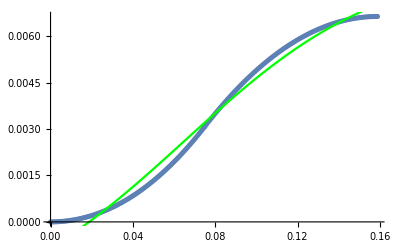

```mathematica
sol=getPath[10, 0.15, 2,50];
solfit = Fit[sol,{x^2, x^0.5, (x-0.1)^2},x]
nlmfit = Normal[NonlinearModelFit[sol,( b Sin[c x] + d Cos[e x]) ,{a,b,c, d,e},x]]
Show[ListPlot[sol],Plot[nlmfit,{x,0,0.25},PlotStyle->Green]]
```

```mathematica
FourierDCT[sol]//MatrixForm
```

(0.370521 | 0.223182
-0.257089 | -0.154598
0.105038 | 0.0661458
-0.0261561 | -0.0200499
-0.00166674 | 0.00117856
-0.00944698 | -0.00635022
0.0118003 | 0.00725295
-0.0050789 | -0.00370098
-0.000446312 | 0.00031559
-0.00277318 | -0.00192799
0.00425459 | 0.00260286
-0.00214142 | -0.00152419
-0.000201801 | 0.000142695
-0.00126948 | -0.000901848
0.0021702 | 0.00132556
-0.00119291 | -0.00083599
-0.000114192 | 0.0000807459
-0.000709033 | -0.000512771
0.00131155 | 0.000800526
-0.000768079 | -0.000531836
-0.0000732292 | 0.0000517809
-0.000443141 | -0.000325871
0.000876692 | 0.000534898
-0.000540484 | -0.000370484
-0.0000508601 | 0.0000359635
-0.00029753 | -0.000222474
0.000626505 | 0.000382166
-0.000403858 | -0.00027438
-0.0000373302 | 0.0000263964
-0.000209794 | -0.000159615
0.0004695 | 0.000286352
-0.000315101 | -0.000212361
-0.0000285309 | 0.0000201744
-0.000153192 | -0.000118727
0.00036455 | 0.000222321
-0.000253997 | -0.000169909
-0.0000224895 | 0.0000159025
-0.000114751 | -0.0000907418
0.000290946 | 0.000177421
-0.000210015 | -0.000139512
-0.0000181635 | 0.0000128436
-0.0000875781 | -0.0000708104
0.000237338 | 0.000144723
-0.000177224 | -0.000116955
-0.0000149598 | 0.0000105782
-0.0000677435 | -0.0000561539
0.000197084 | 0.000120173
-0.000152069 | -0.0000997268
-0.0000125212 | 8.85382×10^-6
-0.0000528785 | -0.0000450893
0.000166087 | 0.000101269
-0.000132312 | -0.0000862494
-0.0000106217 | 7.51068×10^-6
-0.0000414896 | -0.0000365503
0.000141707 | 0.0000864024
-0.000116484 | -0.0000754925
-9.11339×10^-6 | 6.44414×10^-6
-0.0000325983 | -0.0000298358
0.000122184 | 0.0000744972
-0.000103587 | -0.0000667589
-7.89548×10^-6 | 5.58295×10^-6
-0.0000255435 | -0.0000244698
0.000106304 | 0.0000648141
-0.0000929256 | -0.0000595627
-6.89779×10^-6 | 4.87747×10^-6
-0.0000198658 | -0.0000201201
0.0000932105 | 0.0000568303
-0.0000839995 | -0.0000535564
-6.06984×10^-6 | 4.29202×10^-6
-0.0000152388 | -0.0000165497
0.0000822846 | 0.0000501683
-0.000076443 | -0.0000484862
-5.37496×10^-6 | 3.80067×10^-6
-0.0000114253 | -0.0000135858
0.0000730696 | 0.0000445494
-0.0000699827 | -0.0000441631
-4.78594×10^-6 | 3.38417×10^-6
-8.24974×10^-6 | -0.0000111006
0.0000652225 | 0.0000397649
-0.0000644108 | -0.0000404441
-4.28209×10^-6 | 3.0279×10^-6
-5.58063×10^-6 | -8.99701×10^-6
0.0000584824 | 0.0000356553
-0.0000595674 | -0.0000372191
-3.84775×10^-6 | 2.72077×10^-6
-3.31719×10^-6 | -7.20152×10^-6
0.000052647 | 0.0000320977
-0.0000553274 | -0.000034402
-3.47005×10^-6 | 2.4537×10^-6
-1.38262×10^-6 | -5.65625×10^-6
0.0000475588 | 0.0000289951
-0.0000515919 | -0.0000319248
-3.13964×10^-6 | 2.22006×10^-6
2.84451×10^-7 | -4.31679×10^-6
0.0000430916 | 0.0000262717
-0.0000482812 | -0.0000297337
-2.84869×10^-6 | 2.01433×10^-6
1.73133×10^-6 | -3.14711×10^-6
0.0000391459 | 0.0000238659
-0.0000453318 | -0.0000277846
-2.59086×10^-6 | 1.83201×10^-6
2.9965×10^-6 | -2.11885×10^-6
0.0000356401 | 0.0000217285
-0.000042691 | -0.0000260422
-2.36117×10^-6 | 1.6696×10^-6
4.11058×10^-6 | -1.20884×10^-6
0.0000325083 | 0.000019819
-0.0000403161 | -0.0000244771
-2.15544×10^-6 | 1.52412×10^-6
5.09869×10^-6 | -3.98384×10^-7
0.0000296959 | 0.0000181045
-0.0000381712 | -0.0000230651
-1.97018×10^-6 | 1.39313×10^-6
5.98111×10^-6 | 3.28109×10^-7
0.000027158 | 0.0000165572
-0.0000362266 | -0.000021786
-1.80265×10^-6 | 1.27466×10^-6
6.77487×10^-6 | 9.83331×10^-7
0.000024857 | 0.0000151543
-0.0000344572 | -0.0000206228
-1.65036×10^-6 | 1.16698×10^-6
7.49392×10^-6 | 1.57801×10^-6
0.000022761 | 0.0000138764
-0.0000328417 | -0.0000195613
-1.51137×10^-6 | 1.0687×10^-6
8.15011×10^-6 | 2.12106×10^-6
0.0000208435 | 0.0000127073
-0.000031362 | -0.0000185891
-1.38387×10^-6 | 9.78547×10^-7
8.75325×10^-6 | 2.62012×10^-6
0.0000190814 | 0.0000116332
-0.0000300026 | -0.000017696
-1.26653×10^-6 | 8.95572×10^-7
9.31176×10^-6 | 3.08164×10^-6
0.0000174556 | 0.0000106418
-0.0000287503 | -0.0000168727
-1.15803×10^-6 | 8.18849×10^-7
9.83298×10^-6 | 3.51105×10^-6
0.0000159488 | 9.72325×10^-6
-0.0000275934 | -0.0000161116
-1.05716×10^-6 | 7.47528×10^-7
0.0000103229 | 3.91327×10^-6
0.0000145467 | 8.86847×10^-6
-0.0000265218 | -0.0000154061
-9.6319×10^-7 | 6.81078×10^-7
0.000010787 | 4.29237×10^-6
0.0000132366 | 8.06968×10^-6
-0.0000255268 | -0.00001475
-8.75206×10^-7 | 6.18864×10^-7
0.00001123 | 4.65193×10^-6
0.0000120072 | 7.32018×10^-6
-0.0000246007 | -0.0000141382
-7.92425×10^-7 | 5.60329×10^-7
0.000011656 | 4.99522×10^-6
0.0000108487 | 6.61393×10^-6
-0.0000237367 | -0.0000135662
-7.14266×10^-7 | 5.05062×10^-7
0.0000120687 | 5.32506×10^-6
9.75247×10^-6 | 5.9456×10^-6
-0.0000229286 | -0.0000130299
-6.40151×10^-7 | 4.52655×10^-7
0.0000124714 | 5.64399×10^-6
8.71066×10^-6 | 5.31045×10^-6
-0.0000221711 | -0.0000125258
-5.69571×10^-7 | 4.02748×10^-7
0.0000128671 | 5.95429×10^-6
7.71626×10^-6 | 4.70422×10^-6
-0.0000214595 | -0.0000120504
-5.02041×10^-7 | 3.54996×10^-7
0.0000132586 | 6.25808×10^-6
6.76293×10^-6 | 4.12303×10^-6
-0.0000207893 | -0.000011601
-4.37157×10^-7 | 3.09117×10^-7
0.0000136482 | 6.55729×10^-6
5.84491×10^-6 | 3.56335×10^-6
-0.0000201567 | -0.0000111749
-3.74538×10^-7 | 2.64839×10^-7
0.0000140386 | 6.8537×10^-6
4.95685×10^-6 | 3.02194×10^-6
-0.0000195581 | -0.0000107698
-3.13851×10^-7 | 2.21926×10^-7
0.0000144318 | 7.14899×10^-6
4.09383×10^-6 | 2.49578×10^-6
-0.0000189903 | -0.0000103832
-2.54703×10^-7 | 1.80102×10^-7
0.0000148301 | 7.4448×10^-6
3.25121×10^-6 | 1.98207×10^-6
-0.0000184503 | -0.0000100133
-1.96816×10^-7 | 1.3917×10^-7
0.0000152355 | 7.74267×10^-6
2.4246×10^-6 | 1.47816×10^-6
-0.0000179353 | -9.65818×10^-6
-1.39885×10^-7 | 9.89138×10^-8
0.0000156501 | 8.04415×10^-6
1.60987×10^-6 | 9.81477×10^-7
-0.0000174428 | -9.31601×10^-6
-8.36534×10^-8 | 5.91519×10^-8
0.0000160761 | 8.35072×10^-6
8.0298×10^-7 | 4.89557×10^-7
-0.0000169702 | -8.98511×10^-6
-2.78369×10^-8 | 1.96836×10^-8
0.0000165154 | 8.66387×10^-6)

0.590813 x^2

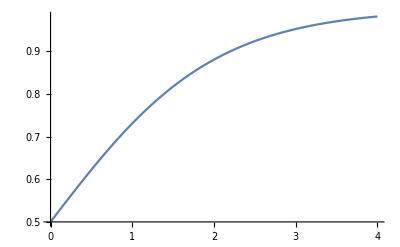

```mathematica
Plot[,{x,0,4}]
```